## Attempt 1

File is from 
[fphysics@facet-srv01 ~/nate]$ pwd
/home/fphysics/nate

```mathematica
raw = Import["/Users/nmajik/Downloads/bowtiedata_LI11_LI18_repeat.mat","IndeterminateValues"->0];
```

Looking at this by hand, find a chunk which looks worthwhile to expand further

```mathematica
data = Flatten[raw[[6]]];
data = StringSplit/@data;
data[[1]]

data =<|
"ele"->#[[6]],
"axis"->#[[7]],
"offset"->ToExpression[#[[10]]],
"error"->ToExpression[#[[12]]]
|>&/@data;

data[[1]]

data = SortBy[data,#ele&];
```

{02/23/2014,10:42,bowtie_gui,Bowtie,BBA,LI11:BPMS:401,X,Measured,offset:,-1.1191,+/-,0.0054,mm}

<|ele→LI11:BPMS:401,axis→X,offset→-1.1191,error→0.0054|>

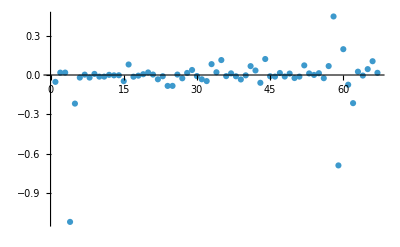

```mathematica
ListPlot[
Select[data,#axis=="X"&][[All,"offset"]],
PlotRange->All
]
```

Hmmm, no... that doesn’t look like the desired plot:
-Graphics-
From http://physics-elog.slac.stanford.edu/facetelog/show.jsp?dir=/2014/09/25.02&pos=2014-02-25T20:30:01

I’m thinking I need to find “ballistic” rather than “bowtie” data

## Attempt 2

```mathematica
raw = Import["/Users/nmajik/Downloads/for_fjd.mat","IndeterminateValues"->0];
```

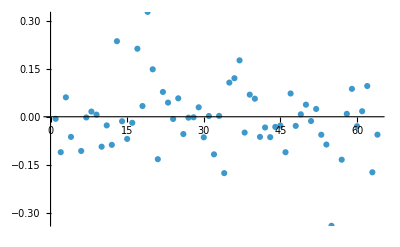

```mathematica
ListPlot[raw[[1,1]]]
```

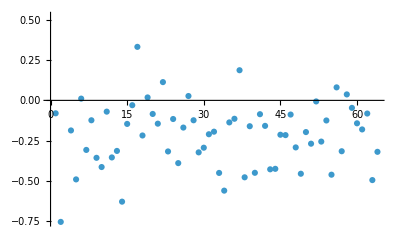

```mathematica
ListPlot[raw[[2,1]]]
```

Also no

## Attempt 3

Fuck it. I hate archeology

Using https://plotdigitizer.com/app

### X

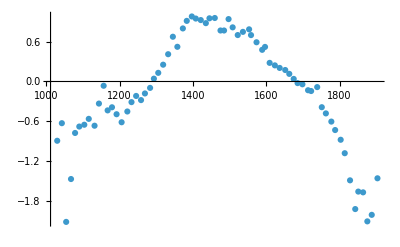

```mathematica
raw = Import["/Users/nmajik/Downloads/plot-data.csv"][[2;;]];

ListPlot[raw]
```

Z values from Bmad

```mathematica
quadZValues = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/quadZValues.json"]//Association
```

<|QM10771→1018.33,QM10781→1018.74,QA11132→1022.05,Q11201→1028.31,QA11265→1034.39,Q11301→1037.63,QM11312→1039.21,QM11358→1046.52,QM11362→1047.17,QM11393→1052.09,Q11401→1053.01,Q11501→1065.35,Q11601→1077.69,Q11701→1090.04,Q11801→1102.38,Q11901→1115.05,Q12201→1129.92,Q12301→1142.26,Q12401→1154.61,Q12501→1166.95,Q12601→1179.29,Q12701→1191.64,Q12801→1203.98,Q12901→1216.65,Q13201→1231.52,Q13301→1243.86,Q13401→1256.21,Q13501→1268.55,Q13601→1280.89,Q13701→1293.24,Q13801→1305.58,Q13901→1318.25,Q14201→1333.12,Q14301→1345.46,Q14401→1357.81,Q14501→1370.15,Q14601→1382.49,Q14701→1394.84,QM14715→1396.88,QM14891→1421.41,Q14901→1421.82,Q15201→1434.72,Q15301→1447.06,Q15401→1459.41,Q15501→1471.75,Q15601→1484.09,Q15701→1496.44,Q15801→1508.78,Q15901→1521.45,Q16201→1536.32,Q16301→1548.66,Q16401→1561.01,Q16501→1573.35,Q16601→1585.69,Q16701→1598.04,Q16801→1610.38,Q16901→1623.05,Q17201→1637.92,Q17301→1650.26,Q17401→1662.61,Q17501→1674.95,Q17601→1687.29,Q17701→1699.64,Q17801→1711.98,Q17901→1724.65,Q18201→1739.52,Q18301→1751.86,Q18401→1764.21,Q18501→1776.55,Q18601→1788.89,Q18701→1801.24,Q18801→1813.58,Q18901→1826.25,Q19201→1841.12,Q19301→1853.46,Q19401→1865.81,Q19501→1878.15,Q19601→1890.49,Q19701→1902.84,Q19801→1915.18,Q19851→1921.57,Q19871→1923.76|>

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

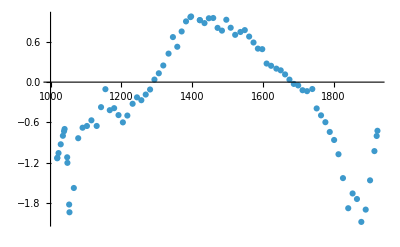

```mathematica
xOffsetInterp = Interpolation[raw,InterpolationOrder->1];

ListPlot[
{
#,
xOffsetInterp[#]
}&/@Values[quadZValues]

]
```

```mathematica
pinkCurveXOffsets =Table[
ele ->xOffsetInterp[quadZValues[ele]] ,
{ele,Keys[quadZValues]}
]//Association;
Export["~/pinkCurveXOffsets.json",pinkCurveXOffsets]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

~/pinkCurveXOffsets.json

### Y

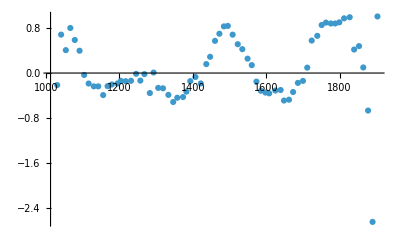

```mathematica
raw = Import["/Users/nmajik/Downloads/plot-data (1).csv"][[2;;]];

ListPlot[raw]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

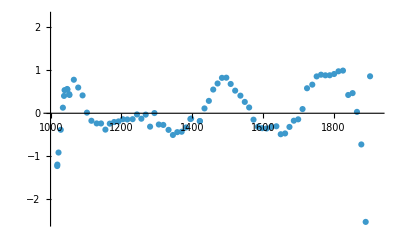

```mathematica
yOffsetInterp = Interpolation[raw,InterpolationOrder->1];

ListPlot[
{
#,
yOffsetInterp[#]
}&/@Values[quadZValues]

]
```

```mathematica
pinkCurveYOffsets =Table[
ele ->yOffsetInterp[quadZValues[ele]] ,
{ele,Keys[quadZValues]}
]//Association;
Export["~/pinkCurveYOffsets.json",pinkCurveYOffsets]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

~/pinkCurveYOffsets.json

## Blue curve

### X

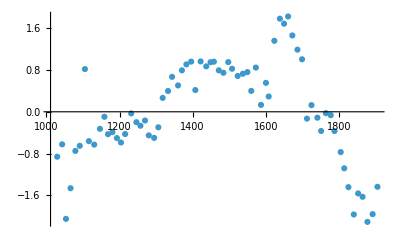

```mathematica
raw = Import["/Users/nmajik/Downloads/plot-data (2).csv"][[2;;]];

ListPlot[raw]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

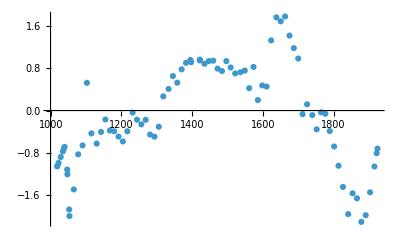

```mathematica
xOffsetInterp = Interpolation[raw,InterpolationOrder->1];

ListPlot[
{
#,
xOffsetInterp[#]
}&/@Values[quadZValues]

]
```

```mathematica
blueCurveXOffsets =Table[
ele ->xOffsetInterp[quadZValues[ele]] ,
{ele,Keys[quadZValues]}
]//Association;
Export["~/blueCurveXOffsets.json",blueCurveXOffsets]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

~/blueCurveXOffsets.json

### Y

```mathematica
raw = Import["/Users/nmajik/Downloads/plot-data (1).csv"][[2;;]];

ListPlot[raw]
```

-Graphics-

```mathematica
yOffsetInterp = Interpolation[raw,InterpolationOrder->1];

ListPlot[
{
#,
yOffsetInterp[#]
}&/@Values[quadZValues]

]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-Graphics-

```mathematica
pinkCurveYOffsets =Table[
ele ->yOffsetInterp[quadZValues[ele]] ,
{ele,Keys[quadZValues]}
]//Association;
Export["~/pinkCurveYOffsets.json",pinkCurveYOffsets]
```

InterpolatingFunction::dmval: Input value {1018.33} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1018.74} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1022.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

~/pinkCurveYOffsets.json